# Homework 4

## Exercise 1

Q = ln(1+P)
Q = I/(5(1+P))
ln(1+P) = I/(5(1+P))
dP/(1+P) = dI/(5(1+P))
5(1+P)dP = 5 dI
dP/dI = 1/(1+P)
dQ/dP = 1/(1+P)
dQ/dI = (∂I/(5(1+P)))/(∂I) + dP/dI
dQ/dI = 1/(5(1+P)) + 1/(1+P)

A rise in income causes prices to rise by 1/(1+P) and quantity to rise by 1/(5(1+P)) + 1/(1+P)

## Exercise 2

Maximize x^(1/3) y^(2/3) s.t. 3 x + 2 y = k
ℒ(x, y, λ) = x^(1/3) y^(2/3) + λ(3 x + 2 y - k) = 0
ℒ_x = 1/3 x^(-2/3) y^(2/3) + 3λ = 0
ℒ_y = 2/3 y^(-1/3) x^(1/3) + 2 λ = 0
ℒ_λ = 3 x + 2 y - k = 0

λ = (-y^(-1/3) x^(1/3))/3
ℒ_x = 1/3 x^(-2/3) y^(2/3) - y^(-1/3) x^(1/3) = 0
= y^(2/3)/(3 x^(2/3)) - x^(1/3)/y^(1/3) = 0
y^(2/3)/(3 x^(2/3)) = x^(1/3)/y^(1/3)
y = 3 x
-3 x + y = 0

ℒ_λ = 3 x + 2 y - k = 0
3 x + 2 y = k

(-3 | 1
3 | 2) (x
y) = (0
k)
(x
y) = 1/(-6 - 3)(2 | -1
-3 | -3) (0
k)
(x
y) = (k/9
k/3)

### Checking my work

```mathematica
Solve[3x + 2y -k == 0 && y== 3x, {x, y}]
```

{{x→k/9,y→k/3}}

## Exercise 3

Explanation of listing 1
	Function cartesianProduct ( set1 : Set , set2 : Set ) → Set :
Here we are defining a function cartesianProduct which takes as it’s argument set1 (whose type is Set) and set2 (whose type is also a set) and which returns a value that is also a set.
		cp ← ∅
We assign the null set to the variable cp
		for x ∈ set1:
Here we take each element of set1, bind it to the variable x and then perform the operations described in the indented section
			for y ∈ set2 :
Here we take each element of set2, bind it to the variable y and then perform the operations described in the indented section
				cp ← cp . union ( {( x , y ) } )
We form the ordered pair (x, y). We then make this a (single element) set (by enclosing it in {}).  We then union this ordered pair to the cp variable.
	return cp
Finally, we return cp.

To demonstrate how the code works, let’s call cartersianProduct({1, 2}, {3, 4}):
Step 1: cp ← ∅  (cp is now ∅)
Step 2: for x ∈ set1: (x is now bound to 1)
	Step 2’: for y ∈ set2 (y is now bound to 3)
		Step 2’’: cp ← ∅.union({(1, 3)})  (cp is now {∅, (1, 3)})
	We now loop back to 2’ with y bound to 4
		Step 2’’: cp ← {∅, (1, 3)}.union({1, 4}) (cp is now {∅, (x1, y1), (x1, y2)})
Having exhausted all elements of set2, we loop back to Step 2. Now x is bound to 2.
	We repeat Step 2’ with x bound to 2 and y bound to 3.
		This results in step 2’’ being executed with x = 2, y = 3
		cp = {∅, (1, 3), (1, 4), {2, 3)}
	We repeat step 2’ with y now bound to 4.
		This reuslts in execution of 2’’ with x bound to 2 and y bound to 4:
		cp = {∅, (1, 3), (1, 4), {2, 3), (2, 4)}

## Exercise 4

X = {Alice, Bert, Chris}
Y = {Algebra, Calculus}
X × Y = {(Alice, Algebra), (Alice, Calculus), (Bert, Algebra), (Bert, Calculus), (Chris, Algebra), (Chris, Calculus)}

binary relation:
Has Taken X × Y: X ↦ Y
that is:
Has Taken {(Alice, Algebra), (Alice, Calculus), (Bert, Algebra), (Bert, Calculus), (Chris, Algebra), (Chris, Calculus)}: {Alice, Bert, Chris} ↦ {Algebra, Calculus}

For example
Has Taken({Calculus}) ↦ {Chris}

The inverse function
Taken By Y × X: Y ↦ X
Taken By {(Algebra, Alice), (Calculus, Alice), (Algebra, Bert), (Calculus, Bert), (Algebra, Chris), (Calculus, Chris)}: {Algebra, Calculus} ↦ {Alice, Bert, Chris}

For example
Taken By({Alice}) ↦ {Calculus}

## Exercise 5

<: {(-1, 0), (-1, 1), (0, 1))
≤: {(-1, -1), (-1, 0), (0, 0), (0, 1), (1, 1)}
=: {(-1, -1), (0, 0), (1, 1)}

< | -1 | 0 | 1
-1 | F | T | T
0 | F | F | T
1 | F | F | F 

≤ | -1 | 0 | 1
-1 | T | T | T
0 | F | T | T
1 | F | F | T

= | -1 | 0 | 1
-1 | T | F | F
0 | F | T | F
1 | F | F | T

## Exercise 6

The power set of the natural numbers are the real number.

1. The complement of any subset of the real numbers are also in the real numbers (for example, the complement of the interval [1, 2] is (-∞, 1) and (2, ∞)).
2. The universal set is the real numbers and its complement (the null set) is also in the set (from previous homerwork)
3. Unions of subsets of the real numbers are also in the real numbers

Therefore it is an algebra.

The μ(A) function is additive because μ(A∪B) = μ(A) + μ(B) (where A and B are disjoint subsets of ℝ). For example, μ([1,10]) + μ(>10) = 0 + ∞ = ∞. Another example: μ([1,10]) + μ([10, 20]) = 0 + 0 = 0.

However, the function is not sigma additive because the union of the subsets of reals is not finite:
μ (∪_(n=1)^∞ ℝ_n) = ∞ 
≠ Σ_(n=1)^∞ μ(ℝ_n) = 0

## Exercise 7

The PMF of the binomial distribution is: (n
k) p^k q^(n-k)
The Expectation is: ∑_(k=0)^n k(n
k) p^k q^(n-k)
The first term in the sum (when k = 0) is 0, so we can rewrite this is as
∑_(k=1)^n k(n
k) p^k q^(n-k)
We can rewrite k (n
k) as n (n - 1
k - 1)
Thus our sum becomes
∑_(k=1)^n n(n-1
k-1) p^k q^(n-k)
We can factor out np using (n - 1) - (k - 1) = n - k.
We obtain:
np ∑_(k=1)^n (n-1
k-1) p^(k - 1)q^((n-1) - (k - 1))
Subsitituting m = n -1  and j = k -1
np∑_(j=0)^m (m
j)p^j q^(m-j)
Using binomial theorem and p + q = 1 we opbtin
np∑_(j=0)^m (m
j)p^j q^(m-j) = np

## Computational Exercise 1

```mathematica
ClearAll[cp, x, y, set1, set2]
cartesianProduct[set1_, set2_] :=Module[{cp = {}, x, y},
Do[
Do[
AppendTo[cp,{x, y}], 
{y, set2}], 
{x, set1}];
Return[cp]]
sixDice = cartesianProduct[Range[1, 6], Range[1,6]]
sumsTo[_, {}, result_] := result;
sumsTo[target_, possibleRolls_, result_] :=(
currentRoll = First[possibleRolls];
currentSum = First[currentRoll] + First[Rest[currentRoll]];
If[currentSum  == target,
(
sumsTo[target, Rest[possibleRolls], Append[result, currentRoll]]),
sumsTo[target, Rest[possibleRolls], result]])
StringForm["Rolls that sum to 1: ``",sumsTo[1, sixDice, {}]]
StringForm["Rolls that sum to 2: ``", sumsTo[2, sixDice, {}]]
StringForm["Rolls that sum to 7: ``", sumsTo[7, sixDice, {}]]
Print["All Possible Sums"]
TableForm[Map[sumsTo[#, sixDice, {}]&, Range[2, 12]], TableHeadings->{Range[2, 12], None}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6}}

Rolls that sum to 1: {}

Rolls that sum to 2: {{1, 1}}

Rolls that sum to 7: {{1, 6}, {2, 5}, {3, 4}, {4, 3}, {5, 2}, {6, 1}}

All Possible Sums

2 | 1
1 |  |  |  |  | 
3 | 1
2 | 2
1 |  |  |  | 
4 | 1
3 | 2
2 | 3
1 |  |  | 
5 | 1
4 | 2
3 | 3
2 | 4
1 |  | 
6 | 1
5 | 2
4 | 3
3 | 4
2 | 5
1 | 
7 | 1
6 | 2
5 | 3
4 | 4
3 | 5
2 | 6
1
8 | 2
6 | 3
5 | 4
4 | 5
3 | 6
2 | 
9 | 3
6 | 4
5 | 5
4 | 6
3 |  | 
10 | 4
6 | 5
5 | 6
4 |  |  | 
11 | 5
6 | 6
5 |  |  |  | 
12 | 6
6 |  |  |  |  |

## Computational Exercise 2

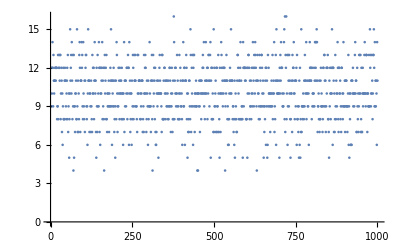

The sample mean is 10.065

The theoretical mean is 10.

The sample variance is  4.93171

The theoretical mean is 5.

4 | 7
5 | 19
6 | 29
7 | 70
8 | 114
9 | 157
10 | 171
11 | 167
12 | 127
13 | 84
14 | 38
15 | 14
16 | 3

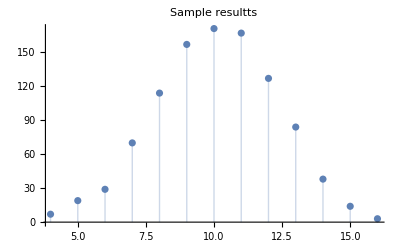

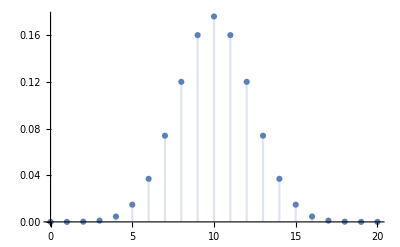

```mathematica
results = RandomVariate[BinomialDistribution[20,0.5], 1000];
ListPlot[results]
StringForm["The sample mean is ``", Mean[results]//N]
StringForm["The theoretical mean is ``", Mean[BinomialDistribution[20, 0.5]]]
StringForm["The sample variance is  ``", Variance[results]//N]
StringForm["The theoretical mean is ``", Variance[BinomialDistribution[20, 0.5]]]
Sort[Tally[results], #1[[1]] < #2[[1]]&]//TableForm
ListPlot[Tally[results], Filling->Axis, PlotLabel->"Sample resultts"]
PDF[BinomialDistribution[20, 0.5], k];
DiscretePlot[%, {k, 0, 20}]
```

## Computational Exercise 3

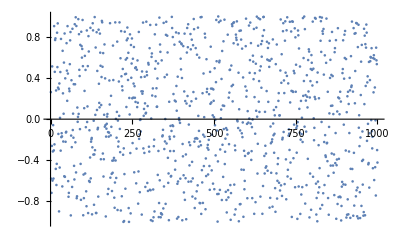

{1,2,3}

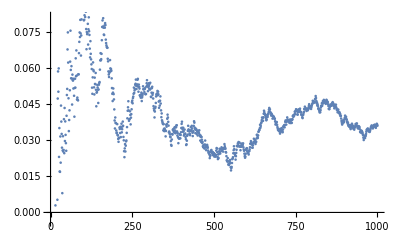

```mathematica
x = RandomVariate[UniformDistribution[{-1,1}],1000];
ListPlot[x]
runningAverage[y_] :=(results = {};
Do[AppendTo[results, Total[Take[y, n]]/n],  {n, Length[y]}];
Return[results]);
runningAverage[{1,3, 5}]
ListPlot[runningAverage[x]]
```